# Simple Relativitic Calculation

```mathematica
c = 299.792458; (*mm ns *)
mp=938.27203;
md=1875.63;
mHe4=3728.4;
mC12=11178;
mO14 = 13048.92;
```

```mathematica
T2γ[T_(*MeV/u*),m_(*MeV/c^2*),A_]:=(T A+m)/m 
γ2T[γ_,m_,A_]:=(γ-1) m/A(* MeV/u*)
γ2β[γ_]:=√(1-1/γ^2)
β2γ[β_]:=1/(√(1-β^2))
β2ToF[β_,l_]:=l/(β c)(*ns, mm*)
T2Bρ[T_(* MeV *),m_(*MeV/c^2*),A_,Z_]:=(√(2m  (A T)+(A T)^2))/(c Z)(* T-m *)
ToF2β[ToF_ (*ns *),l_(* mm*)]:=l/(ToF c)
T2Bρ[m_,Z_,A_,T_]:= m T2γ[T,m,A] T2β[T,m,A] 1/(Z c)
Bρ2T[m_,Z_,A_,Bρ_]:=1/A( √((Bρ Z c)^2+m^2)-m)
```

```mathematica
T2β[T_,m_,A_]:=γ2β[T2γ[T,m,A]]
T2ToF[T_,m_,A_,l_]:=β2ToF[γ2β[T2γ[T,m,A]],l]
ToF2T[ToF_,l_,m_,A_]:=γ2T[β2γ[ToF2β[ToF,l]],m,A]
```

## Sandbox

```mathematica
m28Si=26053.187104;
m30P=27916.95648;
m34Cl=31637.671534;
m44Ti=40936.948536;
m46V=42799.901118;
```

```mathematica
T2Bρ[m28Si,14,14,300]
T2Bρ[m30P,15,15,300]
T2Bρ[m34Cl,17,17,300]
T2Bρ[m44Ti,22,22,300]
T2Bρ[m46V,23,23,400]
```

3.66399

3.66417

3.66408

3.66384

4.28301

```mathematica
Plot[T2Bρ[m46V,23,2 23,T],{T,100,400}]
```

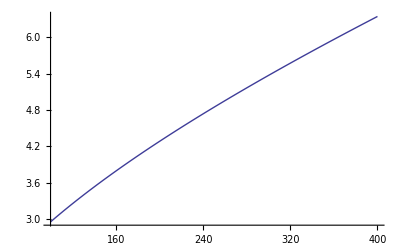

```mathematica
T2Bρ[m,Z,A,T]
```

(0.00333564 (m+A T) √(1-m^2/(m+A T)^2))/Z

```mathematica
Table[(√(T Z (2 m+T Z)))/(c Z),
```

```mathematica
T2β[Bρ2T[mp,1,1,2],mp,1]
```

0.538474

```mathematica
Bρ2T[mp,1,1,2]
```

175.216

```mathematica
Simplify[T2Bρ[m,Z,A,T]c,(m+A T) >0]
```

(1000000 √(A T (2 m+A T)))/Z

```mathematica
T2Bρ[mO14,8,14,260]
```

4.33805

```mathematica
Bρ2T[mO14,8,14,4.2]
```

245.402

```mathematica
T2Bρ[100/2,md,2,1]//N
```

2.07005

2.07005

```mathematica
T2β[T,m,A]
```

√(1-m^2/(m+A T)^2)

```mathematica
ToF2β[11.84555,1510.68469]
β2γ[%]
γ2T[%,mp,1]
ToF2T[11.84555,1510.68469,mp,1]
```

0.4254

1.10497

98.4866

98.4866

```mathematica
β2ToF[γ2β[T2γ[100,mHe4,4]],4698.5]
β2ToF[γ2β[T2γ[230,mHe4,4]],4698.5]
```

36.4979

26.2427

```mathematica
T2ToF[100,mHe4,4,4698.5]
```

36.4979

```mathematica
T2Bρ[260/1.5,mp,1]
```

1.98831

```mathematica
Solve[T2Bρ[T,m,A]==Bρ,T]
```

{{T→(-500000 m-√(22468879468420441 A^2 Bρ^2+250000000000 m^2))/500000},{T→(-500000 m+√(22468879468420441 A^2 Bρ^2+250000000000 m^2))/500000}}

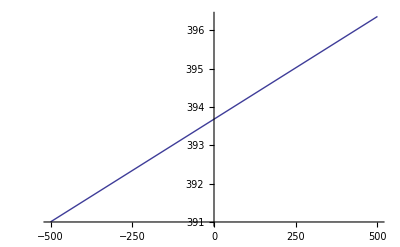

```mathematica
Plot[β2ToF[γ2β[T2γ[260,mp]],73410+x],{x,-500,500}]
```